## Линейный конгруэнтный генератор

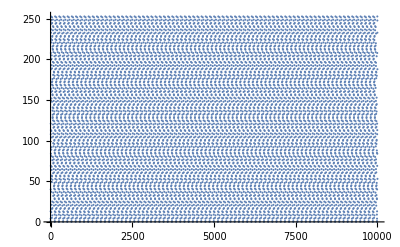
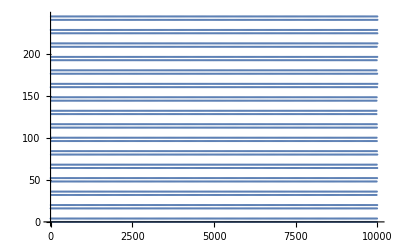
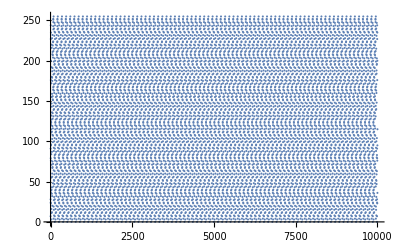
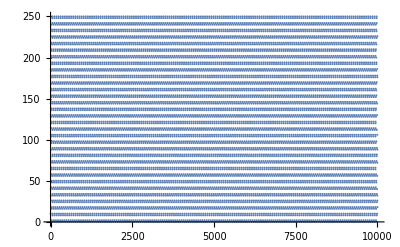
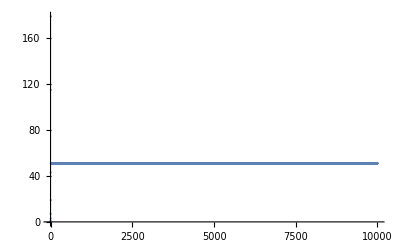
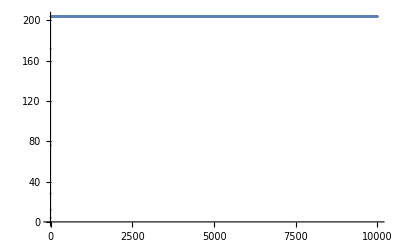
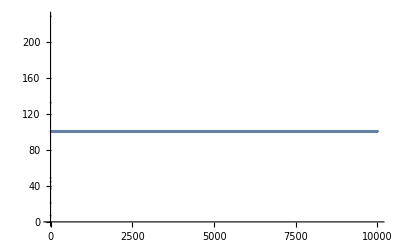
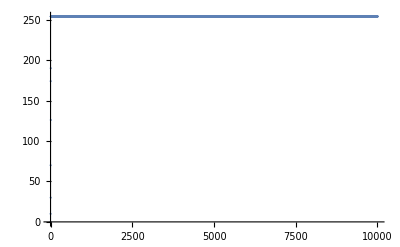
-Graphics-
3
1 | -Graphics-
3
4 | -Graphics-
3
7 | -Graphics-
3
10
-Graphics-
6
1 | -Graphics-
6
4 | -Graphics-
6
7 | -Graphics-
6
10
-Graphics-
9
1 | -Graphics-
9
4 | -Graphics-
9
7 | -Graphics-
9
10
-Graphics-
12
1 | -Graphics-
12
4 | -Graphics-
12
7 | -Graphics-
12
10
-Graphics-
15
1 | -Graphics-
15
4 | -Graphics-
15
7 | -Graphics-
15
10
-Graphics-
18
1 | -Graphics-
18
4 | -Graphics-
18
7 | -Graphics-
18
10

```mathematica
nMax=10000;
mod = 2^8;
lkp[x_,a_,c_,m_]:=RecurrenceTable[{X[n+1]==Mod[(a*X[n]+c),m],X[1]==x},X,{n,1,nMax}];t = Table[{ListPlot[lkp[0,a,c,mod]], a,c}, {a,3,20,3},{c,1,10,3}];
TableForm[t]
```